## Introduction

Tutorial for Gourab

## Manipluate

### Warm up example

```mathematica
f[x_,a_,b_]:=a x^2-b;
Manipulate[Plot[f[x,a,b],{x,-3,3},AxesOrigin->{0,0},LabelStyle->15,AxesLabel->{"x"},],
{a,-2,2},{b,-3,3}]
```

### Our example

#### Grab fixed points

```mathematica
Clear[e,b,k]
v={
e-b Sin[x1-α1]+j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[x2-α2]-j/2 Sin[x2-x1]Cos[θ2-θ1],
e-b Sin[θ1-α1]+k/2 Sin[θ2-θ1]Cos[x2-x1],
e-b Sin[θ2-α2]-k/2 Sin[θ2-θ1]Cos[x1-x2]
}/.{α1->0,α2->π,b->1,j->k,e->0};
TableForm[v]
```

-Sin[x1]-1/2 k Cos[θ1-θ2] Sin[x1-x2]
1/2 k Cos[θ1-θ2] Sin[x1-x2]+Sin[x2]
-Sin[θ1]-1/2 k Cos[x1-x2] Sin[θ1-θ2]
1/2 k Cos[x1-x2] Sin[θ1-θ2]+Sin[θ2]

```mathematica
fp=Solve[v=={0,0,0,0},{x1,x2,θ1,θ2}]
```

{{x1→ConditionalExpression[2 π C[1], C[1]∈ℤ],x2→ConditionalExpression[-2 π C[2], C[2]∈ℤ],θ1→ConditionalExpression[2 π C[3], C[3]∈ℤ],θ2→ConditionalExpression[-2 π C[4], C[4]∈ℤ]},50,{x1→ArcTan[1/2 (-3 k+k^3+6 k (2/3-k^2/(12 (-27 k^4+k^6+3 √3 √1)^(1/3))-(ⅈ k^2)/(4 √3 (1)^(1/3))-((-27 k^4+k^6+3 √3 √1)^(1/3))/(12 k^2)+(ⅈ (-27 k^4+k^6+3 √3 1)^(1/3))/(4 √3 k^2))-5 k^3 (2/3-k^2/(12 1)-1-1/1+(ⅈ 1)/(4 √3 k^2))-4 k (2/3-k^2/(12 1)-1-1+(ⅈ 1)/(4 √3 k^2))^2+8 k^3 (2/3-k^2/(12 (1)^(1/3))-(ⅈ k^2)/(4 √3 (1)^(1/3))-(1)^(1/3)/(12 k^2)+(ⅈ (-27 k^4+k^6+1)^(1/3))/(4 √3 k^2))^2-4 k^3 (2/3-k^2/(12 (1)^(1/3))-(ⅈ k^2)/(4 √3 (1)^(1/3))-((-27 k^4+k^6+3 √3 √1)^(1/3))/(12 k^2)+(ⅈ (-27 k^4+k^6+3 √3 √1)^(1/3))/(4 √3 k^2))^3),√1]+2 π C[1] if C[1]∈ℤ,x2→1,1,θ2→1}}
 |  |  |  |

#### Plot

```mathematica
subC={C[1]->0,C[2]->0,C[3]->0,C[4]->0};
Manipulate[
ListPlot[{x1,x2}/.fp/.subC/.k->k1,
PlotStyle->PointSize[Large],
AxesLabel->{"x1","x2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}}
],
{{k1,0.01},-5,5}
]
```

General::munfl: ArcTan[0.867617-4.12844×10^-16 ⅈ,0.497233-6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.867617+4.12844×10^-16 ⅈ,-0.497233+6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[0.867617-4.12844×10^-16 ⅈ,0.497233-6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcTan[0.867617-4.12844×10^-16 ⅈ,0.497233-6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.867617+4.12844×10^-16 ⅈ,-0.497233+6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[0.867617-4.12844×10^-16 ⅈ,0.497233-6.97751×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: ArcTan[-0.841309+3.65896×10^-16 ⅈ,0.540554-3.20916×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[0.841309-3.65896×10^-16 ⅈ,-0.540554+3.20916×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: ArcTan[-0.841309+3.65896×10^-16 ⅈ,0.540554-3.20916×10^-17 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
subC={C[1]->0,C[2]->0,C[3]->0,C[4]->0};
Manipulate[
p1=ListPlot[{x1,x2}/.fp/.subC/.k->k1,
PlotStyle->PointSize[Large],
AxesLabel->{"x1","x2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

p2=ListPlot[{θ1,θ2}/.fp/.subC/.k->k1,
PlotStyle->PointSize[Large],
AxesLabel->{"θ1","θ2"},
LabelStyle->15,
AxesOrigin->{0,0},
PlotRange->{{-π,π},{-π,π}},
ImageSize->Medium
];

Grid[{{p1,p2}}]
,
{{k1,0.01},-5,5}
]
```

## Region plot

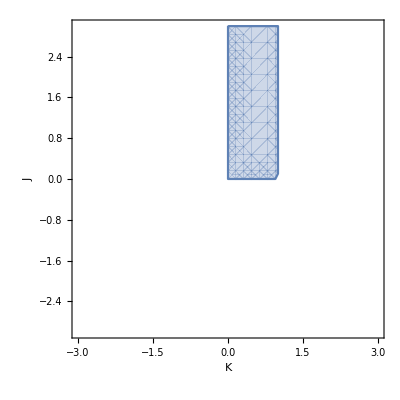

```mathematica
Δ3=k-k^2;
a1=j Sin[k];
RegionPlot[Δ3>0&& a1>0,{k,-3,3},{j,-3,3},FrameLabel->{"K","J"},LabelStyle->15]
```